```mathematica
dir=NotebookDirectory[];
folder="ExampleData";
```

```mathematica
repeats=1;
conc=Table[{0,0.1,0.2,0.4,0.5,0.75,1,2},{i,1,repeats}];
```

```mathematica
proteinDilution=10; (*protein dilution factor before addition to 100μl well*)
proteinConc=4.56/proteinDilution; (*mg·ml^-1 from bradford*)
lysateDilutionInWell=100/20; (*20μl in 100μl assay*)
pathLength=0.26; (*10μl well volume*)
NADHExt=6.22 (*mM^-1 cm^-1*);
```

```mathematica
rangeCheck[r_]:=Module[{},Manipulate[range[r]={p⟦1⟧,q⟦1⟧};Show[dataPlots⟦r⟧,Epilog->{Gray,Opacity[0.2],Rectangle[{p⟦1⟧,-1},{q⟦1⟧,2}]}],{{p,{0,0}},Locator,Appearance->None},{{q,{data⟦1,-1,1⟧,0}},Locator,Appearance->None}]]
```

```mathematica
Table[rangeCheck[i],{i,Length[dataPlots]}]
```

{,,,,,,,}

```mathematica
rangeFolder="linearRanges";
```

```mathematica
ranges=Table[range[i],{i,1,Length[dataPlots]}]
(*ranges = Import[FileNameJoin[{dir,folder,rangeFolder,rangeFileName}]]*)
```

{{0,3.24},{0,2.71},{0,2.09},{0,2.12},{0,2.22},{0,2.08},{0.57,2.48},{1.16,3.73}}

```mathematica
positionNearest[x_]:=(#1&)@@FirstPosition[time,Nearest[time,x]⟦1⟧];
fits=Table[LinearModelFit[data⟦i,positionNearest[ranges⟦i,1⟧];;positionNearest[ranges⟦i,2⟧]⟧,x,x],{i,1,Length[data]}];
rates=-Table[D[fits[[i]][x],x],{i,1,Length[fits]}]*(proteinDilution/(NADHExt*pathLength*proteinConc))
```

{0.102172,0.148063,0.316575,0.397837,0.496549,0.622929,0.572826,0.765753}

```mathematica
(*Export[FileNameJoin[{dir,folder,rangeFolder,rangeFileName}],ranges]*)
```

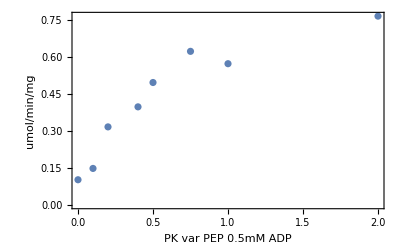

```mathematica
var=StringDelete[fileName,".xlsx"];
ListPlot[Thread[{Flatten[conc],rates}],Axes->False,Frame->True,FrameLabel->{var,"umol/min/mg"},LabelStyle->Directive[Black,FontSize->16],PlotRange->All]
```

```mathematica
rateData=Drop[Thread[{Flatten[conc],rates}]];
headings={{var<>" mM", "V (umol/min/mg)"}};
```

```mathematica
dataForExport=Join[headings,SortBy[rateData,First]];
MatrixForm[dataForExport]
```

(PK var ATP 2.5mM PEP 5mM ADP mM | V (umol/min/mg)
0 | 2.25092
0.1 | 2.20157
0.25 | 2.0353
0.5 | 1.96526
1 | 1.70327
2.5 | 1.44045
5 | 0.938864
10 | 0.358543)

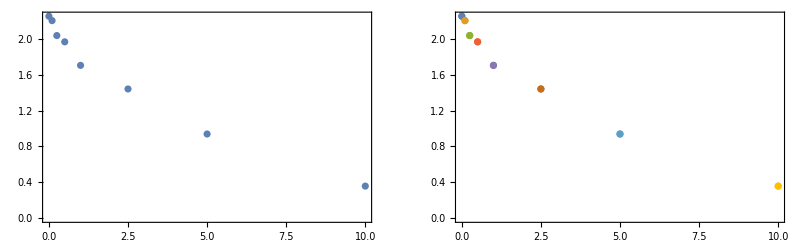

```mathematica
GraphicsRow[{ListPlot[Thread[{DeleteDuplicates@conc[[1]],MeanAround[#[[;;,2]]]&/@GatherBy[rateData,First]}],Axes->False,Frame->True,PlotRange->Full],
ListPlot[GatherBy[rateData,First],Axes->False,Frame->True,PlotRange->All]},ImageSize->Full]
```

### Data formatting:

```mathematica
allDataHeadings={{"PEP","ADP","Pyr","ATP","F16BP","V(umol/min/mg)"}}
```

{{PEP,ADP,Pyr,ATP,F16BP,V(umol/min/mg)}}

#### vary PEP

```mathematica
(*dataFormatted={#[[1]],5,0,0,0,#[[2]]}&/@SortBy[rateData,First]*)
```

#### vary ADP:

```mathematica
(*dataFormatted={2.5,#[[1]],0,0,0,#[[2]]}&/@SortBy[rateData,First]*)
```

#### vary Pyr:

```mathematica
(*dataFormatted={10,2,#[[1]],0,0,#[[2]]}&/@rateData*)
```

#### vary ATP:

```mathematica
(*dataFormatted={2.5,5,#[[1]],0,0,#[[2]]}&/@rateData*)
```

#### vary F16BP:

```mathematica
(*dataFormatted={2.5,5,0,#[[1]],#[[2]]}&/@rateData*)
```

#### For Exporting

```mathematica
rateFolder = "outputRates";
rateFileName = StringDelete[fileName,{".xlsx"," "}]<>".csv";
(*Export[FileNameJoin[{dir,folder,rateFolder,rateFileName}],Join[allDataHeadings,dataFormatted]];*)
```